## Styles and custom color maps

```mathematica
width=2;
framewidth=1.5;
```

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)
OpaqueBox[legend_]:=Graphics[{{White,Opacity[0.5],Rectangle[]},Inset[legend,{0.5,0.6},Center]}]
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;
FrameLabelSize = 12;
PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},
LabelStyle->{Directive[Black,FontSize->FrameLabelSize,FontFamily->"Arial"]},
AspectRatio->0.75,ImageSize->400,(*PlotStyle->styles,*)PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ListLogLinearPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
SetOptions[ListStepPlot,PlotOptions];
PlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],PlotPoints->60,MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"}};
SetOptions[Plot3D,PlotOptions3D];
ListPlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"},ColorFunction->"SunsetColors"};
SetOptions[ListPlot3D,ListPlotOptions3D];
DensityPlotOptions = {PlotPoints->60,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[DensityPlot,DensityPlotOptions];
ListDensityPlotOptions = {PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[ListDensityPlot,ListDensityPlotOptions];
```

```mathematica
Legending`LegendDump`$DefaultMarkerStyle=EdgeForm[Opacity[1]];
```

```mathematica
ColorHelix[z_] := Module[{start,rot,gamma,amp,angle,red,green,blue,min,max},
start=0.6;
rot=1.5;  
angle=2.0*Pi*(start/3.0+rot*z);
amp = 0.15;
red=z+amp(-0.14861 Cos[angle]+1.78277Sin[angle]);green=z+amp(-0.29227 Cos[angle]-0.90649Sin[angle]);blue=z+amp(1.97294*Cos[angle]);
RGBColor[Abs[Sqrt[1-red]],Abs[Sqrt[1-green]],Abs[Sqrt[1-blue]]]
]
```

## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/mnt/workstation/bottomonia_combined_analysis/hnm/qtraj-nlo/qtraj_out_analysis/mathematica

## Data files

```mathematica
dataDir = "run_OO_5.36_kap6";
```

```mathematica
labelMap = Association[
{"run_OO_5.36_kap6"->  "5.36 TeV O+O; κ̂ = 6, γ̂ = 0, T_F = 180 MeV, τ_med = 0.6 fm"}
]
```

<|run_OO_5.36_kap6→5.36 TeV O+O; κ̂ = 6, γ̂ = 0, T_F = 180 MeV, τ_med = 0.6 fm|>

```mathematica
keys=Keys[labelMap];
figureNameMap=Table[keys[[i]]->keys[[i]],{i,1,Length[keys]}]//Association
```

<|run_OO_5.36_kap6→run_OO_5.36_kap6|>

```mathematica
datafile=FileNameJoin[{"..","input",dataDir,"datafile_partial.gz"}];
```

```mathematica
(*datafile = "../input/"<>dataDir<>"/datafile-avg.gz"*)
```

```mathematica
dirName = wd<>"/output/"<>figureNameMap[dataDir];
If[!DirectoryQ[dirName ],CreateDirectory[dirName]];
```

## Read in data

```mathematica
mapData[x_] := {x[[1]],Join[Table[ x[[2]][[i]],{i,1,12,2}],{x[[2,-1]]}],x[[2,-2]]}
```

```mathematica
rawDataAll=mapData/@Partition[Import[FileNameJoin[{wd,datafile}],"Table"],2];
```

Part::partw: Part 9 of {0.779469,0.56641,0,0.433546,0,0,0,0} does not exist.

Part::partw: Part 11 of {0.779469,0.56641,0,0.433546,0,0,0,0} does not exist.

Part::partw: Part 9 of {0,0,1.04525,0,0.587655,0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*rawDataAll=mapData/@Partition[Import[wd<>datafile,"Table"],2];*)
Length[rawDataAll]
```

33364

```mathematica
selectL[lval_]:=Select[rawDataAll,#[[2,7]]==lval&]
```

```mathematica
rawDataS = selectL[0];
Length[rawDataS]
rawDataP = selectL[1];
Length[rawDataP]
```

16686

16678

```mathematica
myR = RandomInteger[{1,Length[rawDataS]}]
rawDataS[[myR ]]
rawDataP[[myR ]]
```

11527

{{4.49691,-1.1621,-0.756053,-0.504072,4.03197,4.02978,-0.504072},{0.813094,0,0,0,{0.813094,0.725667,0,0.593499,0,0,0,0}⟦9⟧,{0.813094,0.725667,0,0.593499,0,0,0,0}⟦11⟧,0},0}

{{4.49691,-0.376795,-0.779599,1.71025,7.66753,0.725181,1.71025},{0,0.587498,0.204932,0,{0,0,0.587498,0,0.204932,0,0,1}⟦9⟧,{0,0,0.587498,0,0.204932,0,0,1}⟦11⟧,1},0}

```mathematica
supData=Transpose[{rawDataS[[All,2,1]](*1S*), rawDataS[[All,2,2]](*2S*), rawDataP[[All,2,3]](*1P*), rawDataS[[All,2,4]](*3S*), rawDataP[[All,2,5]](*2P*), rawDataS[[All,2,6]](*4S*), rawDataS[[All,3]]}];
```

Transpose::nmtx: The first two levels of {{0.779469,0.691608,0.722842,0.737529,0.703117,0.911986,0.695897,0.699634,0.722328,0.681106,0.891445,0.81809,0.717401,0.678712,1,0.699163,0.847701,0.824138,0.882568,0.725537,0.75359,0.745307,«7»,0.689894,0.851593,0.963521,0.684398,0.677928,0.677742,0.764742,0.668063,0.705527,0.776377,0.699109,0.683166,0.870072,0.701372,0.949608,0.967965,0.697492,0.695262,0.720783,0.766718,0.668054,«16636»},«5»,{«1»}} cannot be transposed.

```mathematica
(*metadata and suppression data (1S, 2S, 1P, 3S, 2P, 4S, 3P)*)
mData = rawDataS[[All,1]];
rawData = Transpose[{mData,supData}];
```

Transpose::nmtx: The first two levels of {{{4.49691,0.50725,0.596643,2.62052,10.1832,0.280692,2.62052},{4.49691,-0.358372,1.81109,-0.925901,11.718,5.08913,-0.925901},{4.49691,-0.869214,-0.63988,0.296219,1.37216,3.21582,0.296219},{4.49691,0.909256,0.31197,-0.587407,3.6432,1.04472,-0.587407},«44»,{4.49691,0.740408,0.690659,3.86415,1.32391,3.00537,3.86415},{4.49691,-0.139967,-0.209171,-0.00294574,6.36883,1.17089,-0.00294574},«16636»},(«1»)^(«1»)} cannot be transposed.

```mathematica
bVals=rawData[[All,1,1]]//Union
```

{0.280692,0.50725,0.596643,2.62052,4.49691,10.1832}

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) 
sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444+0.007756249999999999+0.043152361111111114
```

1.

## Integrated results (no feed down)

```mathematica
selectB[i_]:=Select[rawData,#[[1,1]]==bVals[[i]]&] 
rAAvsB[i_]:=selectB[i][[All,2]][[All,1;;6]] ; (*rawData: {{{metadata from ahydro}, {suppression data for (1S, 2S, 1P, 3S, 2P, 4S)}}*)
rAAavgVsB[i_]:=Mean[rAAvsB[i]]
rAAsdevVsB[i_] :=StandardDeviation[rAAvsB[i]]/Sqrt[Length[rAAvsB[i]]]
```

```mathematica
results=ParallelTable[Join[{bVals[[i]]},Riffle[rAAavgVsB[i],rAAsdevVsB[i]]],{i,1,Length[bVals]}]
```

Transpose::nmtx: The first two levels of {{0.769833,0.843906,0.754414,0.840601,0.907108,0.900832,0.89826,0.882676,0.808755,0.799797,0.822567,0.840451,«27»,0.85294,0.823761,0.816391,0.986692,0.924803,0.835948,0.780994,0.798534,0.776409,0.788239,0.796338,«4950»},«5»,{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{{4.71035,-0.00188921,0.248107,-0.19785,1.78847,3.69082,-0.19785},{4.71035,-0.00190926,-0.0889905,-2.54304,15.2865,5.2304,-2.54304},«47»,{4.71035,-0.0133414,-0.228484,2.90144,13.2303,1.60664,2.90144},«4950»},{«1»}^T} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Riffle::list: List expected at position 1 in Riffle[Mean[Transpose[]],ComplexInfinity].

Join::heads: Heads List and Riffle at positions 1 and 2 are expected to be the same.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Riffle::list: List expected at position 1 in Riffle[Mean[Transpose[]],ComplexInfinity].

Join::heads: Heads List and Riffle at positions 1 and 2 are expected to be the same.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Riffle::list: List expected at position 1 in Riffle[Mean[Transpose[]],ComplexInfinity].

Join::heads: Heads List and Riffle at positions 1 and 2 are expected to be the same.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[Mean[Transpose[]],ComplexInfinity].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Join::heads: Heads List and Riffle at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

{Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]],Join[{-0.00188921},Riffle[Mean[Transpose[]],ComplexInfinity]],Join[{0.248107},Riffle[Mean[Transpose[]],ComplexInfinity]],Join[{1.78847},Riffle[Mean[Transpose[]],ComplexInfinity]],Join[{3.69082},Riffle[Mean[Transpose[]],ComplexInfinity]],Join[{4.71035},Riffle[Mean[Transpose[]],ComplexInfinity]]}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
raa1s = pointMap/@results[[All,{1,2,3}]] ;
raa2s = pointMap/@results[[All,{1,4,5}]] ;
raa1p = pointMap/@results[[All,{1,6,7}]] ;
raa3s = pointMap/@results[[All,{1,8,9}]] ;
raa2p = pointMap/@results[[All,{1,10,11}]] ;
raa3p = pointMap/@results[[All,{1,10,11}]] ;
(*raa4s = pointMap/@results[[All,{1,12,13}]] ;*)
```

Part::partw: Part {1,2,3} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

Part::partw: Part {1,4,5} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

Part::partw: Part {1,6,7} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

Part::partw: Part {1,8,9} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

Part::partw: Part {1,10,11} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

Part::partw: Part {1,10,11} of Join[{-0.19785},Riffle[Mean[Transpose[]],ComplexInfinity]] does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {All⟦1⟧,All} cannot be used as a part specification.

```mathematica
comp1=ListLogPlot[{raa1s,raa2s,raa1p,raa3s,raa2p(*,raa4s*)},PlotRange->{{0,16},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"b [fm]","R_pA"},PlotLegends->Placed[LineLegend[{Style["1s",16],Style["2s",16],Style["1p",16],Style["3s",16],Style["2p",16](*,Style["4s",16]*)},LegendMarkerSize->{{60,15}}],{0.2,0.8}]]
```

-Graphics-

## Check distribution functions

```mathematica
metaData = rawData[[All,1]];
supData = rawData[[All,2]];
```

```mathematica
ptData = metaData[[All,5]];
yData = metaData[[All,7]];
```

```mathematica
𝒟=HistogramDistribution[yData,40];
testPlot=DiscretePlot[PDF[𝒟,x],{x,-10,10,.01}];
```

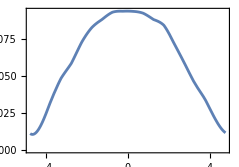
```mathematica
p1 = -Graphics-;
```

```mathematica
f[y_]:= 0.1(1- 2Sqrt[9.46^2+5^2]/5023 Cosh[y])^(13.8)
f2[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/5023 Cosh[y])^(13.8)
f3[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/8160 Cosh[y])^(13.8)
```

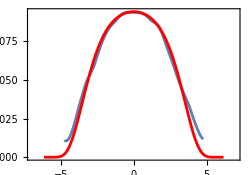

```mathematica
p2=Plot[{f[y](*,f2[y],f3[y]*)},{y,-7,7},PlotStyle->{Blue,Green,Red}];
Show[p1,p2,PlotRange->{{-7,7},All},ImageSize->250]
```

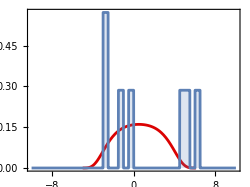

```mathematica
p3=Plot[1.7f[-y+0.5],{y,-5,6.1},PlotStyle->2];
Show[p3,testPlot,ImageSize->250]
```

## Results as a function of p_T averaged over centrality (with feed down)

```mathematica
getWeight[x_] := 1
```

```mathematica
(*mapWithWeight[x_] :=Join[ 1splitHyperfine[ x[[2]][[1;;9]] ],{x[[2,7]]}]*)
```

```mathematica
mapWithWeight[x_] := splitHyperfine[ x[[2]][[1;;7]] ]
```

```mathematica
(*selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&] *)
```

```mathematica
(*selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&]*)
```

```mathematica
selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
weightedList[ptmin_,ptmax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ptmin,ptmax]];
res=selectPTweighted[ptmin,ptmax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_]:= Module[{wl,num,qweights},
wl=weightedList[ptmin,ptmax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsPT[ptmin_,ptmax_]:=Module[{wl},
wl = weightedList[ptmin,ptmax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsPT[ptmin_,ptmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax];
err= nAAsdevVsPT[ptmin,ptmax];
Table[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

### -1.93 < y < 1.93

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
ymin = -1.93;
ymax = 1.93;
```

```mathematica
binwidth=2.5;
ptmax = 30;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of {{0.769833,0.843906,0.754414,0.840601,0.907108,0.900832,0.89826,0.882676,0.808755,0.799797,0.822567,0.840451,«27»,0.85294,0.823761,0.816391,0.986692,0.924803,0.835948,0.780994,0.798534,0.776409,0.788239,0.796338,«4950»},«5»,{«1»}} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of {{{4.71035,-0.00188921,0.248107,-0.19785,1.78847,3.69082,-0.19785},{4.71035,-0.00190926,-0.0889905,-2.54304,15.2865,5.2304,-2.54304},«47»,{4.71035,-0.0133414,-0.228484,2.90144,13.2303,1.60664,2.90144},«4950»},{«1»}^T} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::take: Cannot take positions 1 through 9 in Append.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::take: Cannot take positions 1 through 9 in Append.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa1p = naavsptData[[All,{1,4}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa2p = naavsptData[[All,{1,8}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

```mathematica
ptPlot=ListPlot[{naa1s,naa1p,naa2s,naa2p,naa3s},Joined->True,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotRange->{{0,25},All},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - χ_b(1P)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - χ_b(2P)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax],ImageSize->600]
```

-Graphics-

```mathematica
Export[wd<>"/output/RpA_vs_pT_CentralRap.pdf",ptPlot]
```

/home/sawin/Desktop/qtraj-nlo/mathematica/output/RpA_vs_pT_CentralRap.pdf

```mathematica
fileName =dirName<>"/rpavspt-central.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### -5 < y < -2.5

```mathematica
ymin = -5;
ymax = -2.5;
```

```mathematica
binwidth=2.5;
ptmax = 22;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::take: Cannot take positions 1 through 9 in Append.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa1p = naavsptData[[All,{1,4}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa2p = naavsptData[[All,{1,8}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

```mathematica
ptPlot=ListPlot[{naa1s,naa1p,naa2s,naa2p,naa3s},Joined->True,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotRange->{{0,20},All(*{0.0,1.5}*)},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - χ_b(1P)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - χ_b(2P)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax],ImageSize->600]
```

-Graphics-

```mathematica
Export[wd<>"/output/RpA_vs_pT_BackwardRap.pdf",ptPlot]
```

/home/sawin/Desktop/qtraj-nlo/mathematica/output/RpA_vs_pT_BackwardRap.pdf

```mathematica
fileName =dirName<>"/rpavspt-backward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### 1.5 < y < 4

```mathematica
ymin = 1.5;
ymax = 4;
```

```mathematica
binwidth=2.5;
ptmax = 23;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::take: Cannot take positions 1 through 9 in Append.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa1p = naavsptData[[All,{1,4}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa2p = naavsptData[[All,{1,8}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

```mathematica
ptPlot=ListPlot[{naa1s,naa1p,naa2s,naa2p,naa3s},Joined->True,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotRange->{{0,20},All(*{0.0,1.5}*)},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - χ_b(1P)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - χ_b(2P)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax],ImageSize->600]
```

-Graphics-

```mathematica
Export[wd<>"/output/RpA_vs_pT_ForwardRap.pdf",ptPlot]
```

/home/sawin/Desktop/qtraj-nlo/mathematica/output/RpA_vs_pT_ForwardRap.pdf

```mathematica
fileName =dirName<>"/rpavspt-forward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

## Results as a function of y averaged over centrality and p_T (with feed down)

#### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] := splitHyperfine[ x[[2]][[1;;6]] ]
(*mapWithWeight[x_] := Join[ splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]*)
```

```mathematica
selectWeights[ymin_,ymax_]:=getWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
selectYweighted[ymin_,ymax_]:=mapWithWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
weightedList[ymin_,ymax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ymin,ymax]];
res = selectYweighted[ymin,ymax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsY[ymin_,ymax_]:= Module[{wl,num,qweights},
wl=weightedList[ymin,ymax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsY[ymin_,ymax_]:=Module[{wl},
wl = weightedList[ymin,ymax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsY[ymin_,ymax_]:=Module[{avg,err},
avg = nAAavgVsY[ymin,ymax];
err= nAAsdevVsY[ymin,ymax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Results

```mathematica
binwidth=0.5;
ymax =5;
(* flip y here due to inverse in hydro setup *)
naavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N];
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(«9»[])/Mean[«1»],«9»[]}]⟦All,-1⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

MapThread::mptd: Object Transpose[]/Mean[Transpose[]] at position {2, 1} in MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partd: Part specification MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]⟦All,-1⟧ is longer than depth of object.

Part::partw: Part 3 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 4 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 5 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 6 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 7 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 8 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 9 of (MapThread.MapThread[Append,{(Transpose«1»«1»)/Mean[«1»],«1»}]⟦All,«1»⟧)/Total[MapThread[Append,{Power[«2»] Transpose[],Transpose[]}]⟦All,-1⟧] does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Transpose[]/Mean[Transpose[]],Transpose[]}]]/(√2) does not exist.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
naa1s =naavsyData[[All,{1,2}]] ;
naa1p = naavsyData[[All,{1,4}]] ;
naa2s = naavsyData[[All,{1,3}]] ;
naa2p = naavsyData[[All,{1,8}]] ;
naa3s = naavsyData[[All,{1,7}]] ;
```

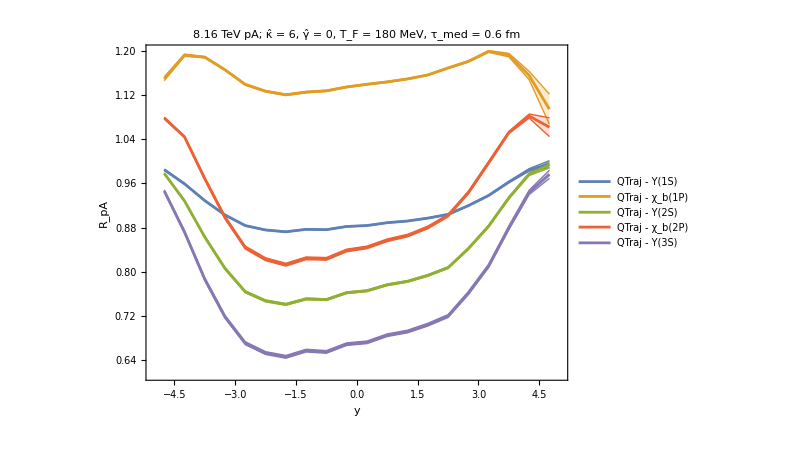

```mathematica
yPlot=ListPlot[{naa1s,naa1p,naa2s,naa2p,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"y","R_pA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - χ_b(1P)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - χ_b(2P)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{{-5,5},All},PlotLabel->labelMap[dataDir]]
```

```mathematica
Export[wd<>"/output/RpA_vs_y.pdf",yPlot]
```

/home/sawin/Desktop/qtraj-nlo/mathematica/output/RpA_vs_y.pdf

```mathematica
fileName =dirName<>"/rpavsy.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvsy={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvsy]
```